#### 0. Define helper functions

```mathematica
(*assumptions*)
$Assumptions = ka>0 && kb >0 && f≥0 && kon≥ 0 &&  k1off>0&& k2off>0 && f1>0 && f2>0;
$MaxExtraPrecision = 200;
```

```mathematica
(*==========================*)
(*delta function*)
Delta[m_, n_]:=DiscreteDelta[m-n]
(*theta function*)
Theta[m_, m0_:0]:=UnitStep[m-m0]
(*translate function*)
(*return one d index*)
Trans[m_, n_]:=m*(N0+1)+n+1
BackTrans[ii_]:= {IntegerPart[Max[(ii-1)/(N0+1),0]], Mod[ii-1, N0+1]}

(*force function*)
Kf[m_, F_,f_]:=If[m==0,0,Exp[F/(m f)]];

(*check if x is interter*)
integerQ[x_]:=x==Round[x]
```

```mathematica
(*==========================*)
Clear[DecodeEntry]
(*DecodeEntry[m1_,n1_, m2_, n2_]:=
(k1off Kf[m1+1, F, f1] * (m1+1)Delta[m1+1, m2]Delta[n1-1, n2]Theta[n1-1]Theta[N0, m1+1]+
k2off Kf[m1+1, F, f2] *(m1+1)Delta[m1+1, m2]Delta[n1,n2]Theta[N0, m1+1]+
k1on*(n1+1)Delta[m1-1,m2]Delta[n1+1, n2]Theta[m1-1,1]Theta[N0, n1+1]+
k2on*(N0-m1-n1+1)Delta[m1-1, m2]Delta[n1, n2]Theta[m1-1,1]-
(k1off Kf[m1, F, f1] *m1+k2off Kf[m1, F, f2]*m1 +n1*k1on + (N0-m1-n1)*k2on)Delta[m1,m2]Delta[n1,n2])Theta[N0, m1+n1]Theta[N0, m2+n2]Theta[m2,1]Theta[m1,1];*)

DecodeEntry[m1_,n1_, m2_, n2_]:=
(k1off Kf[m1+1, F, f1] * (m1+1)Delta[m1+1, m2]Delta[n1-1, n2]Theta[n1-1]Theta[N0, m1+1]+
k2off Kf[m1+1, F, f2]*(m1+1)Delta[m1+1, m2]Delta[n1,n2]Theta[N0, m1+1]+
kon*(n1+1)Delta[m1-1,m2]Delta[n1+1, n2]Theta[m1-1,1]Theta[N0, n1+1]+
kon*(N0-m1-n1+1)Delta[m1-1, m2]Delta[n1, n2]Theta[m1-1,1]-
(k1off Kf[m1, F, f1]*m1+k2off Kf[m1, F, f2]*m1 + (N0-m1)*kon)Delta[m1,m2]Delta[n1,n2])Theta[N0, m1+n1]Theta[N0, m2+n2]Theta[m2,1]Theta[m1,1];

Clear[Entry];
Entry[ii_, jj_]:=
DecodeEntry[BackTrans[ii][[1]], BackTrans[ii][[2]], BackTrans[jj][[1]], BackTrans[jj][[2]]]
```

#### 1. Linear solver

```mathematica
N0=10;
Clear[solverN, solver]
Clear[k2off, F, koon, check, k1off, f1, f2]
solverN[k2off_, F_, kon_, check_:False]:=Module[{threshold=10^(-4), k1off=1,f1=4012/1500,f2=4012/2000},
If[Abs[F]<threshold,
PTable=Table[{i,N[Binomial[N0, i]k1off^i k2off^(N0-i)/(k1off+k2off)^N0]},{i,0,N0}],
PTable =solver[k2off, F, kon, k1off, f1, f2, check,False]];
If[Abs[Sum[PTable[[i, 2]],{i,1, N0+1}]-1]>threshold, Print["total probability not equal 1, sum=", Sum[PTable[[i, 2]],{i,1, N0+1}]]];
PTable
]


solver[k2off_, F_, kon_, k1off_, f1_, f2_, check_:False, simplify_:True]:=Module[{},

(*matrix generator*)
Clear[DecodeEntryN];
DecodeEntryN[m1_,n1_, m2_, n2_]:=
(k1off Kf[m1+1, F, f1] * (m1+1)Delta[m1+1, m2]Delta[n1-1, n2]Theta[n1-1]Theta[N0, m1+1]+
k2off Kf[m1+1, F, f2]*(m1+1)Delta[m1+1, m2]Delta[n1,n2]Theta[N0, m1+1]+
kon*(n1+1)Delta[m1-1,m2]Delta[n1+1, n2]Theta[m1-1,1]Theta[N0, n1+1]+
kon*(N0-m1-n1+1)Delta[m1-1, m2]Delta[n1, n2]Theta[m1-1,1]-
(k1off Kf[m1, F, f1]*m1+k2off Kf[m1, F, f2]*m1 + (N0-m1)*kon)Delta[m1,m2]Delta[n1,n2])Theta[N0, m1+n1]Theta[N0, m2+n2]Theta[m2,1]Theta[m1,1];

Clear[EntryN];
EntryN[ii_, jj_]:=
DecodeEntryN[BackTrans[ii][[1]], BackTrans[ii][[2]], BackTrans[jj][[1]], BackTrans[jj][[2]]];


(*matrix*)
Clear[A];
A = Table[0, {i,(N0+1)^2}, {j,(N0+1)^2}];
For[i=1, i<(N0+1)^2+1,i++,{
For[j=1, j<(N0+1)^2+1, j++, {
A[[i, j]] = EntryN[i, j]
}]
}];

(*state vector*)
Clear[x,t,i];
X = Table[x[i], {i, (N0+1)^2}];

(*vec b*)
Clear[B];
B= Table[0,{i,(N0+1)^2}];
B[[Trans[N0, 0]]]=-1;


(*linear system*)
Clear[system];
system={A.X==B};

(*solve it*)
Clear[sol];
If[ NumberQ[k2off],If[IntegerQ[k2off], sol=LinearSolve[A, B],
sol=LinearSolve[A, B, Method->"Multifrontal"]], sol=LinearSolve[A, B]];

(*load the solution*)
Clear[Q1Table,PTable];
Q1Table = Table[If[simplify, Simplify[sol[[Trans[1, i]]]], sol[[Trans[1, i]]]], {i, 0 ,N0}];
(*If[check, Print["Q1 Table=", Q1Table]];*)

PTable = Table[{i-1, k1off Kf[1,F,f1]*Q1Table[[i-1]]*Theta[i, 2]+k2off  Kf[1,F,f2]*Q1Table[[i]]*Theta[N0, i]},{i, 1, N0+1}];

If[check, Print["P Table=", PTable]];
If[check,
{Print["prob. table=", PTable];
Print["binomal tab=", Table[N[Binomial[N0, i]k1off^i k2off^(N0-i)/(k1off+k2off)^N0],{i,0,N0}]];
Print["no-rebind mean=", Sum[k1off Kf[i, F, f1]/(k2off Kf[i, F, f2]+k1off Kf[i, F, f1]),{i,1, N0}],
", calculated mean=",Sum[(i-1)*PTable[[i, 2]],{i,1, N0+1}] ];
Print["no-rebind std=", Sqrt[Sum[k1off Kf[i, F, f1] k2off Kf[i, F, f2]/(k2off Kf[i, F, f2]+k1off Kf[i, F, f1])^2,{i,1, N0}]],
", calculated std=", Sqrt[Sum[(i-1)^2*PTable[[i, 2]],{i,1, N0+1}]-Sum[(i-1)*PTable[[i, 2]],{i,1, N0+1}]^2]];
}
];
(*calculate the mean*)
Clear[nMean, nStd];
nMean = Sum[(i-1)*PTable[[i,2]],{i,1,N0+1}];
nStd = Sqrt[Sum[(i-1)^2*PTable[[i,2]],{i,1,N0+1}]-nMean^2];

(*return the mean and std*)
(*{nMean, nStd}*)
PTable
]
```

```mathematica
N0=4;
solver[kb, f, kon, ka, f1, f2, False, False];
```

```mathematica
N0=10;
solverN[1.0, 1.0, 1.0]
```

{{0,0.00122094},{1,0.0116719},{2,0.050208},{3,0.127976},{4,0.214053},{5,0.245485},{6,0.195495},{7,0.106747},{8,0.038248},{9,0.00812056},{10,0.000775782}}

```mathematica
N0=10;
solverN[2.0, 0, 0, True]
```

{{0,0.0173415},{1,0.0867076},{2,0.195092},{3,0.260123},{4,0.227608},{5,0.136565},{6,0.0569019},{7,0.0162577},{8,0.00304832},{9,0.000338702},{10,0.0000169351}}

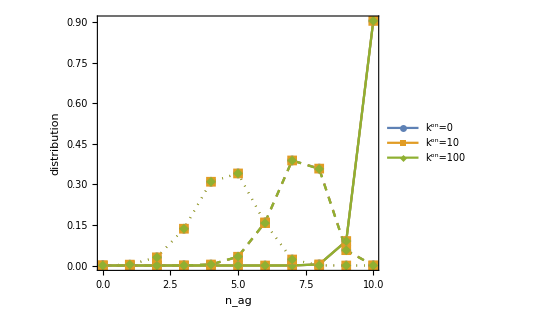

```mathematica
N0=10;
Show[
ListPlot[{solverN[0.01, 0, 0],solverN[0.01, 0, 10],solverN[0.01, 0, 100]}, Filling->None, Joined->True, PlotMarkers->{Automatic,10},PlotLegends->Placed[{"k^on=0","k^on=10","k^on=100"}, {0.3,0.7}], PlotRange->All],
ListPlot[{solverN[0.01, 10N0, 0],solverN[0.01, 10N0, 10],solverN[0.01, 10N0, 100]}, Filling->None, Joined->True, PlotMarkers->{Automatic,10},PlotStyle->Dashed
],
ListPlot[{solverN[0.01, 20N0, 0],solverN[0.01, 20N0, 10],solverN[0.01, 20N0, 100]}, Filling->None, Joined->True, PlotMarkers->{Automatic,10}, PlotStyle->Dotted],

Frame->True,AspectRatio->0.8,
FrameLabel->{"n_ag", "distribution"},
FrameStyle->Directive[14]
]
```

```mathematica
Sqrt[3000/(0.3/1.3)]
```

114.018

#### Exact evaluation of Fisher information

```mathematica
Clear[getFisherInfo]
getFisherInfo[n0_, k2off_, F_, kon_, k1off_, f1_, f2_ ]:=
Module[{},
N0=n0;
Clear[kb,  pTable, dpTable, info];
pTable = solver[kb, F, kon, k1off, f1, f2,False, False][[All, 2]];
dpTable = D[D[Log[pTable], kb], kb];
info=-kb^2Sum[pTable[[i]] dpTable[[i]], {i, 1, Length[pTable]}];
Clear[pTable, dpTable];
info = info/. kb->k2off;
info
]
getFisherInfo[3, 1.0,10, 5, 1, f1=4012/1500,f2=4012/2000 ]
```

0.638379

#### Numerical approximation of Fisher information

```mathematica
Clear[NgetFisherInfo]
NgetFisherInfo[n0_, k2off_, F_, kon_, de_: 1/ 1000, check_:False]:=Module[{},
Clear[info, prob0, prob1, prob2];
N0=n0;
prob0=solverN[k2off, F, kon][[All, 2]];
prob1 = solverN[k2off Exp[de], F, kon][[All, 2]];
If[N0>15,
{prob2 = solverN[k2off Exp[-de], F, kon][[All, 2]];
info = Sum[( (prob2[[ix]]-prob1[[ix]])/(2 de))^2/prob0[[ix]] , {ix, 1, N0+1}]},
info = Sum[( (prob0[[ix]]-prob1[[ix]])/(de))^2/prob0[[ix]] , {ix, 1, N0+1}]
];
Clear[prob0, prob1, prob2];
info
]
```

```mathematica
N[NgetFisherInfo[5, 1.0,10, 5], 5]
```

1.11372

```mathematica
getFisherInfo[2, kbx,10, 5, 1, f1=4012/1500,f2=4012/2000 ]
```

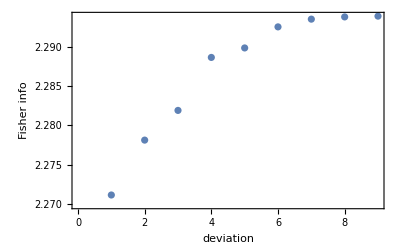

```mathematica
inxTable = {10,21, 30,76, 100, 300, 1000, 3000, 10000};
ListPlot[Table[NgetFisherInfo[1.0, 10, 3, de=1/inxTable[[inx]]],{inx, 1, Length[inxTable]} ],Frame->True, FrameLabel->{"deviation", "Fisher info"}]
```

```mathematica
Table[{nni, NgetFisherInfo[nni, Exp[-2.0], 500, 0]*1000/nni}, {nni, 1, 10}]
```

{{1,6.39641×10^-24},{2,1.08646×10^-10},{3,2.34589×10^-6},{4,0.00031838},{5,0.00596576},{6,0.042941},{7,0.180076},{8,0.537437},{9,1.27335},{10,2.55665}}

#### Gaussian approximation

```mathematica
Clear[etaF, nMeanF, nVarF, nSensF, nVarSensF, gaussianApprox]
etaF[ka_, kb_, f_, f1_:4012/1500, f2_:4012/2000]:=1/(1+kb Kf[1, f, f2] / (ka Kf[1,f, f1])) 
nMeanF[n0_,ka_,kb_,F_]:=Sum[etaF[ka, kb, F/i],{i,1, n0}];
nVarF[n0_,ka_,kb_,F_]:=Sum[etaF[ka , kb, F/i](1-etaF[ka, kb, F/i]), {i, 1, n0}];
nSensF[n0_, ka_, kb_, F_]:=nVarF[n0, ka, kb, F];
nVarSensF[n0_, ka_, kb_, F_]:=(Sum[ etaF[ka , kb, F/i](1-etaF[ka, kb, F/i])(1-2etaF[ka, kb, F/i]), {i, 1, n0}]/ nVarF[n0, ka, kb, F])^2/2;
gaussianApprox[n0_, kb_, F_, ka_:1, alpha_:1]:= nSensF[n0, ka, kb, F]  + alpha nVarSensF[n0, ka, kb, F];
gaussianApprox[10, 1, 0, 1]
```

5/2

```mathematica
nlist =Table[i, {i, 1,15}];
infolistN2 = Table[{nlist[[in]],NgetFisherInfo[nlist[[in]],Exp[-2.0], 500, 0]}, {in, 1, Length[nlist]}]
```

{{1,6.39641×10^-27},{2,2.17293×10^-13},{3,7.03767×10^-9},{4,1.27352×10^-6},{5,0.0000298288},{6,0.000257646},{7,0.00126053},{8,0.0042995},{9,0.0114602},{10,0.0255665},{11,0.0498891},{12,0.0877381},{13,0.142049},{14,0.215058},{15,0.30812}}

```mathematica
nlist =Table[i, {i, 10,20}];
infolistN2 = Table[{nlist[[in]],1000NgetFisherInfo[nlist[[in]],Exp[-2.0], 500, 0]/nlist[[in]]}, {in, 1, Length[nlist]}]
```

{{10,2.55665},{11,4.53538},{12,7.31151},{13,10.9268},{14,15.3613},{15,20.5413},{16,26.3764},{17,32.6918},{18,39.3629},{19,46.2521},{20,53.2345}}

```mathematica
nlist =Table[i, {i, 10,20}];
infolistNNeg2 = Table[{nlist[[in]],1000NgetFisherInfo[nlist[[in]],Exp[2.0], 500, 0]/nlist[[in]]}, {in, 1, Length[nlist]}]
```

{{10,0.0477931},{11,0.0860057},{12,0.14135},{13,0.216448},{14,0.313309},{15,0.433317},{16,0.577844},{17,0.746185},{18,0.938615},{19,1.15462},{20,1.39343}}

```mathematica
nlist =Table[i, {i, 6,20}];
infolistNNeg5 = Table[{nlist[[in]],1000NgetFisherInfo[nlist[[in]],Exp[-5.0], 500, 0]/nlist[[in]]}, {in, 1, Length[nlist]}]
```

{{6,0.855799},{7,3.504},{8,9.88},{9,21.1295},{10,36.4968},{11,53.5624},{12,69.7379},{13,83.4022},{14,94.0255},{15,101.771},{16,107.1},{17,110.505},{18,112.451},{19,113.31},{20,113.369}}

```mathematica
nlist =Table[i, {i, 25,50, 5}];
infolistNNeg2s = Table[{nlist[[in]],1000NgetFisherInfo[nlist[[in]],Exp[2.0], 500, 0]/nlist[[in]]}, {in, 1, Length[nlist]}]
```

General::munfl: (2.47331×10^-157)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.56633×10^-164)^2 is too small to represent as a normalized machine number; precision may be lost.

{{25,2.89045},{30,4.77608},{35,6.9021},{40,9.15391},{45,11.4513},{50,13.7409}}

```mathematica
nlist =Table[i, {i, 25,50, 5}];
infolistN0s = Table[{nlist[[in]],1000NgetFisherInfo[nlist[[in]],Exp[0.0], 500, 0]/nlist[[in]]}, {in, 1, Length[nlist]}]
```

{{25,19.5562},{30,30.9376},{35,42.8023},{40,54.4427},{45,65.4876},{50,75.7751}}

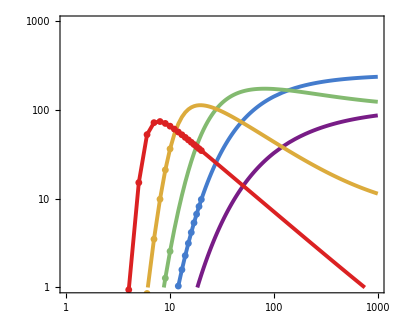
```mathematica
fig0 =-Graphics-
```

-Graphics-

```mathematica
colorlist =Table[ ColorData["Rainbow"][i], {i, 0, 1, 1/4}]
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.266122, 0.486664, 0.802529],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.863512, 0.670771, 0.236564],RGBColor[0.857359, 0.131106, 0.132128]}

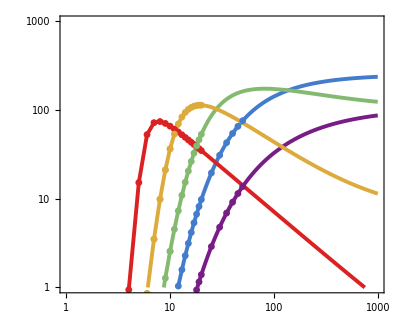

```mathematica
Show[fig0,
ListLogLogPlot[{{25,19.556164101374044},{30,30.9375738087123},{35,42.80233890670997},{40,54.442665293729654},{45,65.48755528053533},{50,75.77508207389303}},
PlotStyle->colorlist[[2]], PlotMarkers->{Automatic, Small}
],
ListLogLogPlot[{{10,2.556645454362931},{11,4.535375406410232},{12,7.311505973959507},{13,10.92683835725723},{14,15.361297486403226},{15,20.541342723915},{16,26.37638944578555},{17,32.691805411539775},{18,39.36294879891029},{19,46.2521220893296},{20,53.2344717715039}}, PlotStyle->colorlist[[3]], PlotMarkers->{Automatic, Small}],
ListLogLogPlot[{{10,0.047793135101381},{11,0.08600574649621888},{12,0.14134987735634552},{13,0.21644779978695913},{14,0.31330904027321527},{15,0.4333169316137078},{16,0.5778438301439347},{17,0.746184696934196},{18,0.9386148386239864},{19,1.1546236871408402},{20,1.3934251533284656},
{25,2.890454634785575},{30,4.776079528041928},{35,6.902101989911398},{40,9.153906084727483},{45,11.451265657337409},{50,13.740903811912077}},
PlotStyle->colorlist[[1]], PlotMarkers->{Automatic, Small}
],
ListLogLogPlot[{{6,0.8557991353532852},{7,3.5040022261774215},{8,9.879999995422828},  {9,21.129503292229685},{10,36.496790636070706},{11,53.56237460678884},{12,69.73788132466572},{13,83.40224036881476},{14,94.0255125371918},{15,101.77116395871133},{16,107.10007606453806},{17,110.50455854191634},{18,112.45115760198041},{19,113.31023200216558},{20,113.3694860237782}},
PlotStyle->colorlist[[4]], PlotMarkers->{Automatic, Small}
]
]
```